```mathematica
Clear["Global `*"]
```

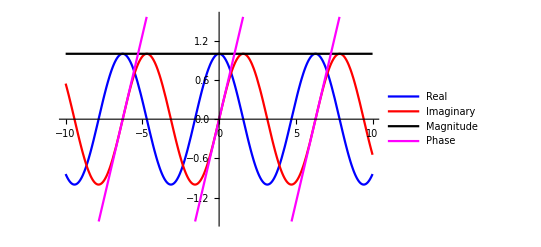

```mathematica
Plot[{Re[Exp[ⅉ t]],Im[Exp[ⅉ t]],Abs[Exp[ⅉ t]], Arg[Exp[ⅉ t]]}, {t,-10,10}, PlotStyle->{{Thick, Blue},{Thick, Red},{Thick, Black}, {Thick, Magenta}}, PlotRange->{-π/2,π/2},
PlotLegends-> {"Real", "Imaginary", "Magnitude", "Phase"}]
(*ListPlot[Table[{x,f[x]},{f,{Sin,Cos,Log}},{x,0,10,0.5}],PlotLegend->{"Sine","Cosine","Log"},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic]*)
```

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5},AnimationRunning->False]
```

```mathematica
ListAnimate[Table[Plot[Sin[n x],{x,0,10}],{n,5}], AnimationRunning->False]
```

```mathematica
Animate[Plot[Re[ⅇ^(ⅉ(2π) t)], {t,-1,b}, PlotStyle->{Thick, Blue},PlotRange-> {{-1,1}, {-1,1}}],{b,-1+.01, 1}, AnimationRunning->False]
```

```mathematica
Animate[Show[Plot[Re[Exp[ⅉ t]],{t,0,4π}],Graphics[Disk[{t,Cos[t]},0.1]],Frame->True,PlotRange->{{0.0001,10},{-2,2}},ImageSize->Automatic],{t,0,4π},AnimationRunning->False]
```

```mathematica
Animate[Show[Graphics[Circle[{0,0},1]],Graphics[{Red,EdgeForm[{Black}],Disk[{Re[Exp[ⅉ t]],Im[Exp[ⅉ t]]},0.045]}],Frame->True,PlotRange->{{-2,2},{-2,2}},ImageSize->Automatic],{t,0,4π},AnimationRunning->False]
```



```mathematica
ω=1;
ParametricPlot[{Re[Exp[ⅉ ω t]], Im[Exp[ⅉ ω t]]}, {t, 0, 2 π}]
```